# Excitation dynamics of interacting Rydberg atoms in small lattices employing Ising model. César Muro.

Lattices of  atoms at high energy levels, i.e. Rydberg atoms, are very suitable platforms for studying quantum many-body dynamics, taking into account  interactions by external driving fields, strong or weak interactions among the atoms, and dissipation processes such as dephasing or spontaneous decay. Moreover, in recent years, Rydberg atoms have been an attractive model for the physical implementation of quantum information processing and communication. 
In this script, we intend to reproduce the dynamics excitation of a one-dimensional lattice of Rydberg atoms by employing the Hamiltonian
                                                                                                                       H=Ω∑_(k=1)^N σ_x^(k)+β/4∑_(k >l)^N ((1+σ_z^(k))(1+σ_z^(l)))/(|k-l|^γ)
where Ω is the Rabi frequency of the driving laser field,  σ_x^(k) and σ_z^(k) are the Pauli matrices, β the strength interaction between the atoms, and N the number of sites of the lattice. We consider two cases: weak Rydberg interaction  β<<Ω, and strong Rydberg interaction β>>Ω. We take ℏ=1, and γ=6 ( van der Waals interaction). To analyze the dynamics of the excitations , we construct the evolution operator U(t)=e^(-i*H*t), to write |ψ(t) >=e^(-i*H*t)|ψ(0)>. Then we calculate the mean number of excitations with the inversion operator ∑_(k=1)^N (1+σ_z^(k))/2.

## Definition of spin operators and Hamiltonian

Depending on the number of sites will be the dimensions of the Hilbert space of our operators. Moreover, the spin operator (σ_(x,z))^(k)  must act only on a spin k and have trivial action on all other spins. Thus we define

```mathematica
SpinQ[S_]:=IntegerQ[2S]&&S≥0;
op[S_?SpinQ,n_Integer,k_Integer,a_?MatrixQ]/;1<=k<=n&&Dimensions[a]=={2*S+1,2*S+1}:=KroneckerProduct[IdentityMatrix[(2*S+1)^(k-1),SparseArray],a,IdentityMatrix[(2S+1)^(n-k),SparseArray]]
```

Now we define the Pauli operators

```mathematica
sx[S_?SpinQ,n_Integer,k_Integer]/;1<=k<=n:=op[S,n,k,PauliMatrix[1]];
sz[S_?SpinQ,n_Integer,k_Integer]/;1<=k<=n:=op[S,n,k,PauliMatrix[3]];
```

and the Hamiltonian

```mathematica
H[S_?SpinQ,n_Integer/;n>=3,Ω_,β_]:=Ω*Sum[sx[S,n,k],{k,n}]+ β/4*Sum[(IdentityMatrix[2^n]+sz[S,n,k]).(IdentityMatrix[2^n]+sz[S,n,Mod[k+1,n,1]])/(Abs[Mod[k+1,n,1]-k]^γ),{k,n}]
```

whose variables are the spin S, the number n of sites, the Rabi frequency Ω, and the strength β.

### Number of sites and initial ground state

Let us define the number of sites, the γ parameter

```mathematica
ns=3;
γ=6;
```

and the initial ground-state of the system

```mathematica
sList=Table[{0,1},{ns}];
init=Fold[Flatten[KroneckerProduct[#1,#2]]&,sList[[1]],sList[[2;;]]];
```

## Weak Rydberg interaction

In this case  β<<Ω. We study the excitations in a time range of {t, 0, 100} . We fix Ω = 3.0, and β=0.3, to obtain

```mathematica
tf=150;
Ω=3;
β=0.3;
```

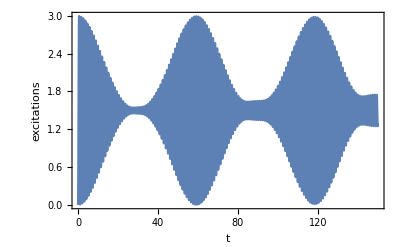

```mathematica
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,Frame->True,PlotRange->All,FrameLabel->{"t","excitations"}]
```

We observe that the population shows fast Rabi oscillations and a long time decay of the oscillations with subsequent revivals.

```mathematica
Clear[tf,Ω,β]
```

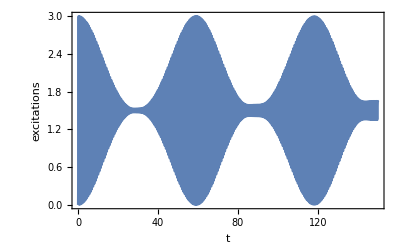

```mathematica
tf=150;
Ω=5;
β=0.3;
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"t","excitations"}]
```

Increasing Rabi frequency increases the number of oscillations.

Now, if we increase the number of sites :

```mathematica
ns=6;
sList=Table[{1,0},{ns}];
init=Fold[Flatten[KroneckerProduct[#1,#2]]&,sList[[1]],sList[[2;;]]];
```

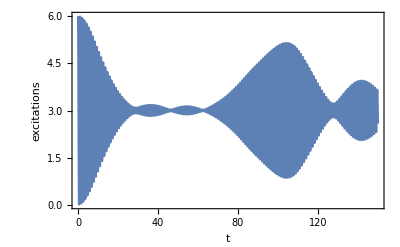

```mathematica
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,Frame->True,PlotRange->All,FrameLabel->{"t","excitations"}]
```

We observe that the number of oscillations is decreasing.

## Strong Rydberg interaction

In this case  Ω<<β. We study the excitations in a time range of {t, 0, 100} . For this case, we fix Ω = 0.3, and β=2, to obtain

```mathematica
Clear[sList,ns,tf,Ω,β]
```

```mathematica
ns=3;
sList=Table[{0,1},{ns}];
init=Fold[Flatten[KroneckerProduct[#1,#2]]&,sList[[1]],sList[[2;;]]];
```

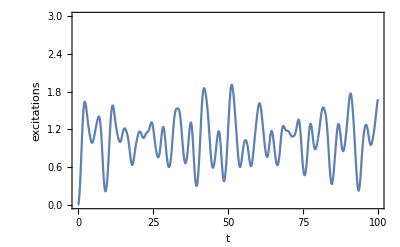

```mathematica
tf=100;
Ω=0.5;
β=2.0;
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,PlotRange->{All,{0,3.0}},Frame->True,FrameLabel->{"t","excitations"}]
```

In this case we have Rydberg excitation blockade, where the dipole-dipole interactions shifts the resonance and prevent excitations.

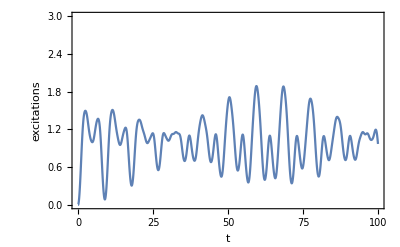

```mathematica
Clear[Ω,β,tf]
tf=100;
Ω=0.5;
β=3.0;
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,PlotRange->{All,{0,3.0}},Frame->True,FrameLabel->{"t","excitations"}]
```

As we increase the factor β then oscillations get lower.
Now, we set the number of sites to 7.

```mathematica
Clear[Ω,β,tf,ns,sList,init]
```

```mathematica
ns=7;
sList=Table[{0,1},{ns}];
init=Fold[Flatten[KroneckerProduct[#1,#2]]&,sList[[1]],sList[[2;;]]];
```

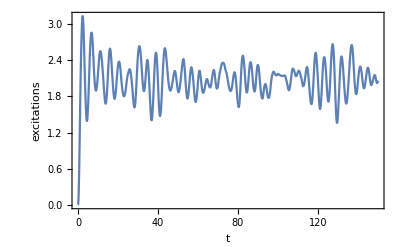

```mathematica
tf=150;
Ω=0.5;
β=4.0;
ListPlot[Transpose@{Table[t,{t,0,tf,0.01}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.01}]},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"t","excitations"}]
```

Now ns=12:

```mathematica
ns=12;
sList=Table[{0,1},{ns}];
init=Fold[Flatten[KroneckerProduct[#1,#2]]&,sList[[1]],sList[[2;;]]];
```

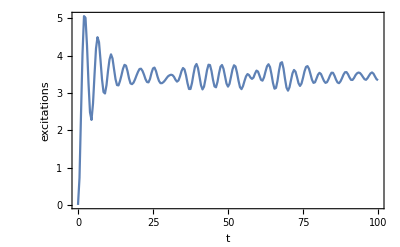

```mathematica
tf=100;
Ω=0.5;
β=5.0;
ListPlot[Transpose@{Table[t,{t,0,tf,0.5}],Table[Conjugate[MatrixExp[-I*H[1/2, ns,Ω,β]*t] . init].Sum[(IdentityMatrix[2^ns]+ sz[1/2, ns, k])/2,{k,1,ns}] . (MatrixExp[-I*H[1/2, ns, Ω,β]*t] . init),{t,0,tf,0.5}]},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"t","excitations"}]
```

## Perspectives

These simple simulations get real physics situations. I expect that if I increase the number of sites in the strong Rydberg regime, I can get this thermalization effect where the excitation oscillations are steady in short times. However, the time for a simulation with a “large” number of ns is too long. 
The following physical situation to study would be the Dicke-Ising model, where we include a quantized cavity field in the Hamiltonian, and also taking into account dissipation processes .

## Relevant bibliography

1. Wu, G., Kurz, M., Liebchen, B., & Schmelcher, P. (2015). Excitation dynamics of interacting Rydberg atoms in small lattices. Physics Letters A, 379(3), 143-148.